## Prelude: Finite difference and derivative approximations

See: wiki/Finite_difference_coefficient

In the following:

s is the stencil, e.g., {-3,-2,-1,0,+1},

d is the order of the derivative, where d≤len(s)

```mathematica
fdCoefficients[d_,s_]:=Inverse[
Join[{Table[1,Length@s]},
Table[s^i,{i,1,Length@s-1}]]].Table[If[d==i,d!,0],{i,0,Length@s-1}]
```

```mathematica
fdDerivative[f_,var_,d_,s_]:=Total[(f/@(var+s))fdCoefficients[d,s]]
```

### Examples

Second order in accuarcy:

```mathematica
Table[fdDerivative[f,n,i,{1,0,-1}]//Echo,{i,0,3}];
```

f[n]

-1/2 f[-1+n]+1/2 f[1+n]

f[-1+n]-2 f[n]+f[1+n]

0

Fourth order in accuarcy:

```mathematica
fdCoefficients[1,{-2,-1,0,1,2}]
fdCoefficients[2,{-2,-1,0,1,2}]
```

{1/12,-2/3,0,2/3,-1/12}

{-1/12,4/3,-5/2,4/3,-1/12}

```mathematica
fdDerivative[f,n,1,{-2,-1,0,1,2}]
fdDerivative[f,n,2,{-2,-1,0,1,2}]
```

1/12 f[-2+n]-2/3 f[-1+n]+2/3 f[1+n]-1/12 f[2+n]

-1/12 f[-2+n]+4/3 f[-1+n]-(5 f[n])/2+4/3 f[1+n]-1/12 f[2+n]

```mathematica
fdCoefficients[4,{-3,-2,-1,0,1}]
```

{1,-4,6,-4,1}

Forward and backward differences:

```mathematica
fdDerivative[f,n,3,{0,1,2,3,4,5}]
```

-(17 f[n])/4+71/4 f[1+n]-59/2 f[2+n]+49/2 f[3+n]-41/4 f[4+n]+7/4 f[5+n]

```mathematica
fdDerivative[f,n,4,{-7,-6,-5,-4,-3,-2,-1,0}]
```

-7/2 f[-7+n]+82/3 f[-6+n]-185/2 f[-5+n]+176 f[-4+n]-1219/6 f[-3+n]+142 f[-2+n]-111/2 f[-1+n]+(28 f[n])/3

### Extrapolation

```mathematica
With[
{derivativeOrder=1,accuracy=4,s=Range[-10,0,1]},
Table[
fdDerivative[f,n,i,s⟦-i-accuracy;;⟧]/i!//Echo,
{i,0,derivativeOrder}
]
]//Total//Expand
(* f[n+1]/.Solve[%==0,f[n+1]]⟦1⟧//Expand *)
%/.Rational[p_,q_]:>If[p<0," - "," + "]<>ToString@Abs@p<>"./"<>ToString@q<>"."
List@@%/.Times->List//Flatten
%/.{f[i_+n]:>If[i>0," * f(m,n+"<>ToString[i]<>")"," * f(m,n-"<>ToString[-i]<>")","??"],f[n]->" * f(m,n)",i_?NumericQ:>If[i<0," - "," + "]<>ToString@Abs@i}/.List->StringJoin
```

f[n]

1/4 f[-4+n]-4/3 f[-3+n]+3 f[-2+n]-4 f[-1+n]+(25 f[n])/12

1/4 f[-4+n]-4/3 f[-3+n]+3 f[-2+n]-4 f[-1+n]+(37 f[n])/12

+ 1./4. f[-4+n]+ - 4./3. f[-3+n]+3 f[-2+n]-4 f[-1+n]+ + 37./12. f[n]

{ + 1./4.,f[-4+n], - 4./3.,f[-3+n],3,f[-2+n],-4,f[-1+n], + 37./12.,f[n]}

+ 1./4. * f(m,n-4) - 4./3. * f(m,n-3) + 3 * f(m,n-2) - 4 * f(m,n-1) + 37./12. * f(m,n)

## Maximal slicing in spherical symmetry

Maximal slicing in spherical symmetry corresponds to solving an elliptic 1D PDE (i.e., an ODE with two BC),

1/r^2∂/(∂r)(r^2∂/(∂r)α)=α s(r).

In particular, the source term reads:

s(r)=K_1^2+2 K_2^2+κ_g(ρ+J),  where  J=J_1+2 J_2.

The boundary conditions are Neumann’s on the left (α'=0) and Dirichelt’s on the right (α=1).

#### Example: Gaussian ρ_ADM to be used for the maximal slicing

```mathematica
ϕGR[r_,λ_]:=1+Erf[r/(√2 λ)]/(2 r);
𝔻[r_,λ_]:= 8π ϕGR[r,λ]Exp[-r^2/(2 λ^2)] 1/(((2π)^(1/2)λ)^3);
ρADM[r_,λ_]:=𝔻[r,λ]/ϕGR[r,λ]^6;
```

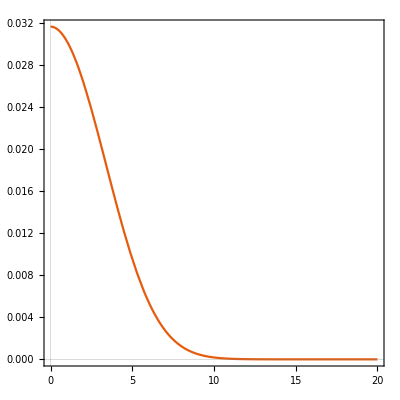

```mathematica
Plot[ρADM[r,3],{r,10^-6,20},PlotRange->Full,AspectRatio->1,PlotTheme->"Scientific"]
```

Find the maximal slicing for the example ρ_ADM in Mathematica,

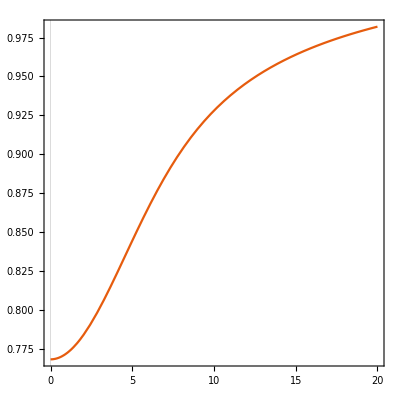

```mathematica
Block[{s,sol},
s[r_]:=ρADM[r,3];
αsol=NDSolveValue[{
α''[r]+2/r α'[r]== α[r]s[r],
α'[10^-6]==3,α[30]==1
},α,{r,10^-6,60}];
Plot[αsol[r],{r,10^-6,20},AspectRatio->1,PlotTheme->"Scientific"]
]
```

## The linear finite-difference algorithm (2nd order in accuarcy)

Here we verify the verification of Algorithm 11.3 from Burden & Faires (2016) Numerical Analysis.
(see Section “Finite-Difference Methods for Linear Problems” on p. 700)

The differential equation we want to solve reads:

```mathematica
DE=-y''[x]+P[x] y'[x]+Q[x]y[x]+R[x];
```

```mathematica
fdD=1;fdG=1; (* the required accuracy specified by the finite difference depth *)
```

#### The finite differences

Convert DE to finite difference equation using central FD derivatives:

```mathematica
fdDE=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,Range[-fdD,fdD,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,Range[-fdD,fdD,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

-1/2 y[-1+n]+1/2 y[1+n]

y[-1+n]-2 y[n]+y[1+n]

h^2 R_n-w_(-1+n)-1/2 h P_n w_(-1+n)+2 w_n+h^2 Q_n w_n-w_(1+n)+1/2 h P_n w_(1+n)

Convert DE to  finite difference equation using forward FD derivatives on the left boundary:

```mathematica
fdDE$L=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,Range[-1,fdG,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,Range[-1,fdG,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

-1/2 y[-1+n]+1/2 y[1+n]

y[-1+n]-2 y[n]+y[1+n]

h^2 R_n-w_(-1+n)-1/2 h P_n w_(-1+n)+2 w_n+h^2 Q_n w_n-w_(1+n)+1/2 h P_n w_(1+n)

Convert DE to  finite difference equation using backward FD derivatives on the right boundary:

```mathematica
fdDE$R=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,-Range[-1,fdG,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,-Range[-1,fdG,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

-1/2 y[-1+n]+1/2 y[1+n]

y[-1+n]-2 y[n]+y[1+n]

h^2 R_n-w_(-1+n)-1/2 h P_n w_(-1+n)+2 w_n+h^2 Q_n w_n-w_(1+n)+1/2 h P_n w_(1+n)

#### The linear system to solve

```mathematica
fdN=5;
```

```mathematica
fdSys=Table[ (* we assume that Subscript[w, n] starts at n == -1 *)
CoefficientList[If[n==0,fdDE$L,If[n==fdN,fdDE$R,fdDE]]/.Subscript[w, n_]:>x^(n+2),x,fdN+4],
{n,0,fdN}
];
Row[{fdSys⟦All⟧//MatrixForm,"·",Transpose@{Join[{1},Table[Subscript[w, i],{i,-1,fdN+1}]]}//MatrixForm,
" == ",Table[0,{i,0,fdN}]//MatrixForm},BaseStyle->Medium]
Row[{fdSys⟦All,3;;-2⟧//MatrixForm,"·",Transpose@{Table[Subscript[w, i],{i,0,fdN}]}//MatrixForm,
" == ",Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R]/.Subscript[w, n_]:>Style[Subscript[w, n],Red]//MatrixForm},BaseStyle->Medium]
```

(h^2 R_0 | -1-(h P_0)/2 | 2+h^2 Q_0 | -1+(h P_0)/2 | 0 | 0 | 0 | 0 | 0
h^2 R_1 | 0 | -1-(h P_1)/2 | 2+h^2 Q_1 | -1+(h P_1)/2 | 0 | 0 | 0 | 0
h^2 R_2 | 0 | 0 | -1-(h P_2)/2 | 2+h^2 Q_2 | -1+(h P_2)/2 | 0 | 0 | 0
h^2 R_3 | 0 | 0 | 0 | -1-(h P_3)/2 | 2+h^2 Q_3 | -1+(h P_3)/2 | 0 | 0
h^2 R_4 | 0 | 0 | 0 | 0 | -1-(h P_4)/2 | 2+h^2 Q_4 | -1+(h P_4)/2 | 0
h^2 R_5 | 0 | 0 | 0 | 0 | 0 | -1-(h P_5)/2 | 2+h^2 Q_5 | -1+(h P_5)/2)·(1
w_-1
w_0
w_1
w_2
w_3
w_4
w_5
w_6) == (0
0
0
0
0
0)

(2+h^2 Q_0 | -1+(h P_0)/2 | 0 | 0 | 0 | 0
-1-(h P_1)/2 | 2+h^2 Q_1 | -1+(h P_1)/2 | 0 | 0 | 0
0 | -1-(h P_2)/2 | 2+h^2 Q_2 | -1+(h P_2)/2 | 0 | 0
0 | 0 | -1-(h P_3)/2 | 2+h^2 Q_3 | -1+(h P_3)/2 | 0
0 | 0 | 0 | -1-(h P_4)/2 | 2+h^2 Q_4 | -1+(h P_4)/2
0 | 0 | 0 | 0 | -1-(h P_5)/2 | 2+h^2 Q_5)·(w_0
w_1
w_2
w_3
w_4
w_5) == (w_L (1+(h P_0)/2)-h^2 R_0
-h^2 R_1
-h^2 R_2
-h^2 R_3
-h^2 R_4
w_R (1-(h P_5)/2)-h^2 R_5)

#### Neumann BC on the left

Here we use the Neumann BC on the left with the vanishing derivative so that w_L==w_-1==w_1. Hence, (h P_0)/2 cancels out in the first raw.

```mathematica
fdSys:=Table[(* we assume that Subscript[w, n] starts at n == -1 *)
CoefficientList[If[n==0,fdDE$L,If[n==fdN,fdDE$R,fdDE]]/.Subscript[w, -1]->Subscript[w, 1]/.Subscript[w, n_]:>x^(n+2),x,fdN+4],
{n,0,fdN}
];
Row[{fdSys⟦All,3;;-2⟧//MatrixForm,"·",Transpose@{Table[Subscript[w, i],{i,0,fdN}]}//MatrixForm,
" == ",Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R]/.Subscript[w, n_]:>Style[Subscript[w, n],Red]//MatrixForm},BaseStyle->Medium]
```

(2+h^2 Q_0 | -2 | 0 | 0 | 0 | 0
-1-(h P_1)/2 | 2+h^2 Q_1 | -1+(h P_1)/2 | 0 | 0 | 0
0 | -1-(h P_2)/2 | 2+h^2 Q_2 | -1+(h P_2)/2 | 0 | 0
0 | 0 | -1-(h P_3)/2 | 2+h^2 Q_3 | -1+(h P_3)/2 | 0
0 | 0 | 0 | -1-(h P_4)/2 | 2+h^2 Q_4 | -1+(h P_4)/2
0 | 0 | 0 | 0 | -1-(h P_5)/2 | 2+h^2 Q_5)·(w_0
w_1
w_2
w_3
w_4
w_5) == (-h^2 R_0
-h^2 R_1
-h^2 R_2
-h^2 R_3
-h^2 R_4
w_R (1-(h P_5)/2)-h^2 R_5)

The above tridiagonal linear system should be solved using the Crout factorization (Algorithm 6.7).

## The linear finite-difference algorithm (4th order in accuarcy)

The differential equation we are interested in:

```mathematica
DE=-2(y''[x]-P[x] y'[x]-Q[x]y[x]-R[x]);
fdD=1;fdG=1; (* FD depths *)
fdN=5;
```

```mathematica
DE=12(y''[x]-P[x] y'[x]-Q[x]y[x]-R[x]);
fdD=2;fdG=3; (* FD depths *)
fdN=50;
```

Use the following test equation to compare with Randall J. LeVeque (2006) Finite Difference Methods for Differential Equation, 10.1.1.111.1693:

```mathematica
If[False,
DE=12(y''[x]-f[x]);
fdD=2;fdG=3; (* FD depths *)
fdN=5;
]
```

#### The finite differences

Convert DE to finite difference equation using central FD derivatives:

```mathematica
fdDE=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,Range[-fdD,fdD,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,Range[-fdD,fdD,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

1/12 y[-2+n]-2/3 y[-1+n]+2/3 y[1+n]-1/12 y[2+n]

-1/12 y[-2+n]+4/3 y[-1+n]-(5 y[n])/2+4/3 y[1+n]-1/12 y[2+n]

-12 h^2 R_n-w_(-2+n)-h P_n w_(-2+n)+16 w_(-1+n)+8 h P_n w_(-1+n)-30 w_n-12 h^2 Q_n w_n+16 w_(1+n)-8 h P_n w_(1+n)-w_(2+n)+h P_n w_(2+n)

Convert DE to  finite difference equation using forward FD derivatives on the left boundary:

```mathematica
fdDE$L=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,Range[-1,fdG,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,Range[-1,fdG,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

-1/4 y[-1+n]-(5 y[n])/6+3/2 y[1+n]-1/2 y[2+n]+1/12 y[3+n]

11/12 y[-1+n]-(5 y[n])/3+1/2 y[1+n]+1/3 y[2+n]-1/12 y[3+n]

-12 h^2 R_n+11 w_(-1+n)+3 h P_n w_(-1+n)-20 w_n+10 h P_n w_n-12 h^2 Q_n w_n+6 w_(1+n)-18 h P_n w_(1+n)+4 w_(2+n)+6 h P_n w_(2+n)-w_(3+n)-h P_n w_(3+n)

Convert DE to  finite difference equation using backward FD derivatives on the right boundary:

```mathematica
fdDE$R=h^2 DE//.{
f_''[x]:>Echo@fdDerivative[f,n,2,-Range[-1,fdG,1]]/h^2,
f_'[x]:>Echo@fdDerivative[f,n,1,-Range[-1,fdG,1]]/h,
f_[x]:>Subscript[f, n]
}/.{y[n_]:>Subscript[w, n],Subscript[y, n]:>Subscript[w, n]}//Expand//Echo;
```

-1/12 y[-3+n]+1/2 y[-2+n]-3/2 y[-1+n]+(5 y[n])/6+1/4 y[1+n]

-1/12 y[-3+n]+1/3 y[-2+n]+1/2 y[-1+n]-(5 y[n])/3+11/12 y[1+n]

-12 h^2 R_n-w_(-3+n)+h P_n w_(-3+n)+4 w_(-2+n)-6 h P_n w_(-2+n)+6 w_(-1+n)+18 h P_n w_(-1+n)-20 w_n-10 h P_n w_n-12 h^2 Q_n w_n+11 w_(1+n)-3 h P_n w_(1+n)

```mathematica
Subscript[w, n+1]/.Solve[fdDE$R==0,Subscript[w, n+1]]⟦1⟧/.{Subscript[R, n_]:>0,Subscript[P, n_]:>PP[n],Subscript[Q, n_]:>QQ[n]}/.Subscript[w, n_]:>gAlp[m,n]//Simplify
%//CForm
```

(gAlp[m,-3+n] (-1+h PP[n])-2 (gAlp[m,-2+n] (-2+3 h PP[n])-3 gAlp[m,-1+n] (1+3 h PP[n])+gAlp[m,n] (10+5 h PP[n]+6 h^2 QQ[n])))/(-11+3 h PP[n])

(gAlp(m,-3 + n)*(-1 + h*PP(n)) - 2*(gAlp(m,-2 + n)*(-2 + 3*h*PP(n)) - 
        3*gAlp(m,-1 + n)*(1 + 3*h*PP(n)) + gAlp(m,n)*(10 + 5*h*PP(n) + 6*Power(h,2)*QQ(n))))/
   (-11 + 3*h*PP(n))

#### The linear system to solve

```mathematica
fdSys=Table[ (* we assume that Subscript[w, n] starts at n == -1 *)
CoefficientList[If[n==0,fdDE$L,If[n==fdN,fdDE$R,fdDE]]/.Subscript[w, n_]:>x^(n+2),x,fdN+4],
{n,0,fdN}
];
If[fdN≤ 5,Row[{fdSys⟦All⟧//MatrixForm,"·",Transpose@{Join[{1},Table[Subscript[w, i],{i,-1,fdN+1}]]}//MatrixForm,
" == ",Table[0,{i,0,fdN}]//MatrixForm},BaseStyle->Medium]]
If[fdN≤5,Row[{fdSys⟦All,3;;-2⟧//MatrixForm,"·",Transpose@{Table[Subscript[w, i],{i,0,fdN}]}//MatrixForm,
" == ",Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R]/.Subscript[w, n_]:>Style[Subscript[w, n],Red]//MatrixForm},BaseStyle->Medium]]
```

The vector w_n can be evaluated using a linear equation solver for band-diagonal systems (see NR3, section 2.4.2 on pp. 58--61).

If you selected the test DE, compare the results with:

-Graphics-

#### Neumann BC on the left

Now we use the Neumann BC on the left with the vanishing derivative (equivalent to w_L==w_-1==w_1 for FD=2).

```mathematica
bcLeftFD2={Subscript[w, -1]->Subscript[w, 1]};
```

```mathematica
bcLeft=Solve[Echo[fdDerivative[w,0,1,Range[-1,fdG,1]]==0],w[-1]]⟦1⟧/.w[n_]:>Subscript[w, n]
```

-1/4 w[-1]-(5 w[0])/6+(3 w[1])/2-w[2]/2+w[3]/12==0

{w_-1→1/3 (-10 w_0+18 w_1-6 w_2+w_3)}

```mathematica
fdSys:=Table[(* we assume that Subscript[w, n] starts at n == -1 *)
CoefficientList[If[n==0,fdDE$L,If[n==fdN,fdDE$R,fdDE]]/.bcLeft/.Subscript[w, n_]:>x^(n+2),x,fdN+4],
{n,0,fdN}
];
If[fdN≤5,Row[{fdSys⟦All,3;;-2⟧//MatrixForm,"·",Transpose@{Table[Subscript[w, i],{i,0,fdN}]}//MatrixForm,
" == ",Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R]/.Subscript[w, n_]:>Style[Subscript[w, n],Red]//MatrixForm},BaseStyle->Medium]]
```

#### Convert to the compactly stored band-diagonal matrix (to be used by ‘banded.h’)

```mathematica
{Table["i = "<>ToString@n,{n,0,fdN}]};
Table[
Join[
Table[0,{-j}],
Table[fdSys⟦All,3;;-2⟧⟦1+n+If[j<0,-j,0],1+n+If[j>0,j,0]⟧,{n,0,fdN-Abs@j}],
Table[0,{j}]
],{j,-Max[fdD,fdG],Max[fdD,fdG]}
];
{Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R]/.Subscript[w, n_]:>Style[Subscript[w, n],Red]};
Grid[
Join[{{"",Sequence@@Table["j = "<>ToString@j,{j,0,2Max[fdD,fdG]}]}},Transpose@Join[%%%,%%,%]]⟦If[fdN≥10,{1,2,3,4,5,-5,-4,-3,-2,-1},All]⟧,
Dividers->All]/.{Subscript[R, n_]:>0}
```

| j = 0 | j = 1 | j = 2 | j = 3 | j = 4 | j = 5 | j = 6 | 
i = 0 | 0 | 0 | 0 | -170/3-12 h^2 Q_0 | 72 | -18 | 8/3 | 0
i = 1 | 0 | 0 | 58/3+(34 h P_1)/3 | -36-6 h P_1-12 h^2 Q_1 | 18-6 h P_1 | -4/3+(2 h P_1)/3 | 0 | 0
i = 2 | 0 | -1-h P_2 | 16+8 h P_2 | -30-12 h^2 Q_2 | 16-8 h P_2 | -1+h P_2 | 0 | 0
i = 3 | 0 | -1-h P_3 | 16+8 h P_3 | -30-12 h^2 Q_3 | 16-8 h P_3 | -1+h P_3 | 0 | 0
i = 46 | 0 | -1-h P_46 | 16+8 h P_46 | -30-12 h^2 Q_46 | 16-8 h P_46 | -1+h P_46 | 0 | 0
i = 47 | 0 | -1-h P_47 | 16+8 h P_47 | -30-12 h^2 Q_47 | 16-8 h P_47 | -1+h P_47 | 0 | 0
i = 48 | 0 | -1-h P_48 | 16+8 h P_48 | -30-12 h^2 Q_48 | 16-8 h P_48 | -1+h P_48 | 0 | 0
i = 49 | 0 | -1-h P_49 | 16+8 h P_49 | -30-12 h^2 Q_49 | 16-8 h P_49 | 0 | 0 | w_R (1-h P_49)
i = 50 | -1+h P_50 | 4-6 h P_50 | 6+18 h P_50 | -20-10 h P_50-12 h^2 Q_50 | 0 | 0 | 0 | w_R (-11+3 h P_50)

#### Solve the example with the Gaussian ρ_PF

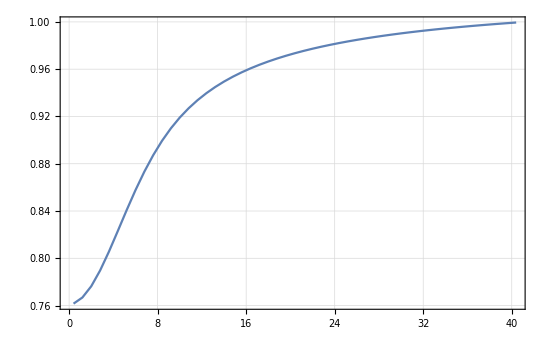

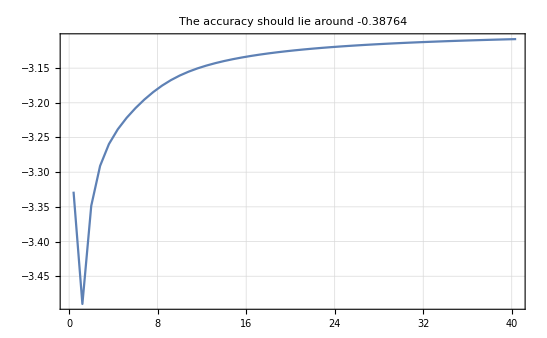

```mathematica
test$Q[r_]=ρADM[r,3];
matA=fdSys⟦All,3;;-2⟧;
vecb=Simplify[-fdSys⟦All,1⟧]+Simplify[-fdSys⟦All,2⟧] Subscript[w, L]+Simplify[-fdSys⟦All,-1⟧] Subscript[w, R];
matA=matA//.{Subscript[w, R]->1,Subscript[P, n_]:>(-2/Subscript[r, n]),Subscript[Q, n_]:>test$Q[Subscript[r, n]],Subscript[R, n_]:>0,h->40/fdN,Subscript[r, n_]:>(n+1/2)h}//N;
vecb=vecb//.{Subscript[w, R]->1,Subscript[P, n_]:>(-2/Subscript[r, n]),Subscript[Q, n_]:>test$Q[Subscript[r, n]],Subscript[R, n_]:>0,h->40/fdN,Subscript[r, n_]:>(n+1/2)h}//N;
vecr=Table[Subscript[r, n],{n,0,fdN,1}]//.{Subscript[w, R]->1,Subscript[P, n_]:>(-2/Subscript[r, n]),Subscript[Q, n_]:>test$Q[Subscript[r, n]],Subscript[R, n_]:>0,h->40/fdN,Subscript[r, n_]:>(n+1/2)h}//N;
matx=Inverse@matA.Transpose@{vecb}//Flatten;
ListLinePlot[Transpose@{vecr,matx},PlotTheme->"Detailed",PlotRange->{Automatic,Full}]
Block[{sol},
αsol=NDSolveValue[{
α''[r]+2/r α'[r]== α[r]test$Q[r],
α'[10^-6]==3,α[40]==1
},α,{r,10^-6,40}];
Quiet@ListLinePlot[Transpose@{vecr,Log10@Abs[matx-(αsol/@vecr)]},
PlotRange->{Automatic,Full},
PlotTheme->"Detailed",PlotLabel->Row@{"The accuracy should lie around ",Log10[(40/fdN)^4]//N}]
]
```

## Banded matrix test (for ‘banded.h’)

A sample equation Ax=b where A is a band matrix:

```mathematica
Partition[{
3,1,0,0,0,0,0,
4,1,5,0,0,0,0,
9,2,6,5,0,0,0,
0,3,5,8,9,0,0,
0,0,7,9,3,2,0,
0,0,0,3,8,4,6,
0,0,0,0,2,4,4
},7];
Transpose@{{7,6,5,4,3,2,1}};
Row@{%%//MatrixForm,"·",Inverse@%%.%//N//Flatten//MatrixForm," == ",%//MatrixForm}
```

(3 | 1 | 0 | 0 | 0 | 0 | 0
4 | 1 | 5 | 0 | 0 | 0 | 0
9 | 2 | 6 | 5 | 0 | 0 | 0
0 | 3 | 5 | 8 | 9 | 0 | 0
0 | 0 | 7 | 9 | 3 | 2 | 0
0 | 0 | 0 | 3 | 8 | 4 | 6
0 | 0 | 0 | 0 | 2 | 4 | 4)·(4.66912
-7.00737
-1.13382
-3.24088
6.29092
10.616
-13.5114) == (7
6
5
4
3
2
1)